## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="RPIa";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_trp2.csv";

mainFolder = "fit_RPIa_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{r5p,Null,Keq substrate}

{0.443,Keq value}

{r5p,Km or S05 substrate}

{0.0031,Km or S05 value}

{{{r5p,Null}},kcat substrates}

{2100,kcat value}

{ara5p,Inhibition or activation constant substrate}

{0.0021,Inhibition or activation constant value}

(r5p^c⇌ru5p__D^c)^RPIa

Null;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | r5p,Null | 0.443 | 0.42085
0.46515 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | r5p | 0.0031 | 0.0029
0.0033 |  | M | 7.5 | 37 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | r5p | Null | 2100. | 1800.
2400. | 1/s | 7.5 | 37 | trishcl | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | ara5p | 0.0021 | 0.0012
0.003 |  | Competitve | r5p | 0.0031 | M | 7.5 | 37 | trishcl | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1};
s05Priorities = Null;
kcatPriorities = {1};
inhibitionPriorities={1};
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(r5p^c⇌ru5p__D^c)^RPIa

Null;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | r5p,Null | 0.443 | 0.42085
0.46515 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | r5p | 0.0031 | 0.0029
0.0033 |  | M | 7.5 | 37 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | r5p | Null | 2100. | 1800.
2400. | 1/s | 7.5 | 37 | trishcl | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | ara5p | 0.0021 | 0.0012
0.003 |  | Competitve | r5p | 0.0031 | M | 7.5 | 37 | trishcl | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_RPIa[c] + r5p[c] <=> E_RPIa[c]&r5p",
				"E_RPIa[c]&r5p <=> E_RPIa[c]&ru5p__D",
				"E_RPIa[c]&ru5p__D <=> E_RPIa[c] + ru5p__D[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((RPIa^c)_^+r5p^c⇌(RPIa^c&r5p^c)_^)^RPIa1,((RPIa^c&ru5p_^D)_^⇌(RPIa^c)_^+ru5p__D^c)^RPIa2,((RPIa^c&r5p^c)_^⇌(RPIa^c&ru5p_^D)_^)^RPIa3}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((RPIa^c)_^+r5p^c⇌(RPIa^c&r5p^c)_^)^RPIa1,Overscript[(RPIa^c&ru5p_^D)_^⇌(RPIa^c)_^+ru5p__D^c, RPIa2],((RPIa^c&r5p^c)_^⇌(RPIa^c&ru5p_^D)_^)^RPIa3};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=2;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

{r5p^c→0}

{ru5p__D^c→0}

{r5p^c→∞}

{ru5p__D^c→∞}

Added inhibition reactions:

{((RPIa^c)_^+ara5p^c⇌(RPIa^c&ara5p^c)_^)^RPIa_Kic_ara5p_1_r5p}

Generating flux equation...

{((RPIa^c&r5p^c)_^-((RPIa^c&ru5p_^D)_^)/K_RPIa3) Volume_c k_RPIa3^⟶}

Volume_c (-(RPIa^c&ru5p_^D)_^ k_RPIa3^⟵+(RPIa^c&r5p^c)_^ k_RPIa3^⟶)

1

2

3

0.080419

4

0.00057

5

0.00017

Simplifying...

6

0.067973

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

{k_RPIa_Kic_ara5p_1_r5p^⟵/k_RPIa_Kic_ara5p_1_r5p^⟶}

```mathematica
FilePrint@dataPathList
```

Priority	r5p[c]	ru5p__D[c]	ara5p[c]	param_RPIa_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt"	0.443
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt"	0.443
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt"	0.443
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt"	0.443
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt"	0.443
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt"	0.443
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt"	0.443
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt"	0.443
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt"	0.443
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt"	0.443
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt"	0.443
1	0.00030999999999999995	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.0909090909090909
1	0.0004913168896629453	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.13680688860321005
1	0.0007786847937679696	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.20076000891310172
1	0.0012341322287158416	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.28474724895080145
1	0.0019559677678886002	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.38686317984685714
1	0.0031	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.49999999999999994
1	0.004913168896629454	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.6131368201531431
1	0.007786847937679696	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.7152527510491985
1	0.012341322287158417	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.7992399910868982
1	0.01955967767888599	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.86319311139679
1	0.030999999999999996	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.9090909090909091
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt"	2100.
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt"	2100.
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt"	2100.
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt"	2100.
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt"	2100.
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt"	2100.
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt"	2100.
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt"	2100.
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt"	2100.
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt"	2100.
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt"	2100.
1	0.00030999999999999995	0	0.00105	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.0625
1	0.0009803060746521974	0	0.00105	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.1741123948954683
1	0.0031	0	0.00105	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.39999999999999997
1	0.009803060746521975	0	0.00105	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.6782688399674104
1	0.030999999999999996	0	0.00105	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.8695652173913043
1	0.00030999999999999995	0	0.0021	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.04761904761904761
1	0.0009803060746521974	0	0.0021	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.1365270594958143
1	0.0031	0	0.0021	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.3333333333333333
1	0.009803060746521975	0	0.0021	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.6125741132772068
1	0.030999999999999996	0	0.0021	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.8333333333333333
1	0.00030999999999999995	0	0.0042	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.03225806451612903
1	0.0009803060746521974	0	0.0042	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.09535767393825997
1	0.0031	0	0.0042	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.24999999999999997
1	0.009803060746521975	0	0.0042	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.513167019494862
1	0.030999999999999996	0	0.0042	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt"	0.7692307692307692
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt"	0.0021
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt"	0.0021
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt"	0.0021
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt"	0.0021
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt"	0.0021
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt"	0.0021
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt"	0.0021
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt"	0.0021
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt"	0.0021
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt"	0.0021
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt"	0.0021

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	8
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateRev_ru5p__D.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	8
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateRev_ru5p__D.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 1.08051749524
best_fit: 0.47405479271
best_fit: 0.930430068455
best_fit: 0.807740358646
best_fit: 0.478243095099

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 3.92997×10^-12 | 1.54446×10^-23 | 4.00874×10^-12 | 9.04907×10^-10 | 0.443 | 0.443
1 | haldaneRatio_1 | 3.92997×10^-12 | 1.54446×10^-23 | 4.00874×10^-12 | 9.04907×10^-10 | 0.443 | 0.443
1 | haldaneRatio_1 | 3.92997×10^-12 | 1.54446×10^-23 | 4.00874×10^-12 | 9.04907×10^-10 | 0.443 | 0.443
1 | haldaneRatio_1 | 3.92997×10^-12 | 1.54446×10^-23 | 4.00874×10^-12 | 9.04907×10^-10 | 0.443 | 0.443
1 | haldaneRatio_1 | 3.92997×10^-12 | 1.54446×10^-23 | 4.00874×10^-12 | 9.04907×10^-10 | 0.443 | 0.443
1 | haldaneRatio_1 | 3.92997×10^-12 | 1.54446×10^-23 | 4.00874×10^-12 | 9.04907×10^-10 | 0.443 | 0.443
1 | haldaneRatio_1 | 3.92997×10^-12 | 1.54446×10^-23 | 4.00874×10^-12 | 9.04907×10^-10 | 0.443 | 0.443
1 | haldaneRatio_1 | 3.92997×10^-12 | 1.54446×10^-23 | 4.00874×10^-12 | 9.04907×10^-10 | 0.443 | 0.443
1 | haldaneRatio_1 | 3.92997×10^-12 | 1.54446×10^-23 | 4.00874×10^-12 | 9.04907×10^-10 | 0.443 | 0.443
1 | haldaneRatio_1 | 3.92997×10^-12 | 1.54446×10^-23 | 4.00874×10^-12 | 9.04907×10^-10 | 0.443 | 0.443
1 | haldaneRatio_1 | 3.92997×10^-12 | 1.54446×10^-23 | 4.00874×10^-12 | 9.04907×10^-10 | 0.443 | 0.443
1 | relRateFor_r5p | 5.19051×10^-12 | 2.69414×10^-23 | 1.08652×10^-12 | 1.19517×10^-9 | 0.0909091 | 0.0909091
1 | relRateFor_r5p | 4.9285×10^-12 | 2.42901×10^-23 | 1.55251×10^-12 | 1.13482×10^-9 | 0.136807 | 0.136807
1 | relRateFor_r5p | 4.56335×10^-12 | 2.08242×10^-23 | 2.10945×10^-12 | 1.05073×10^-9 | 0.20076 | 0.20076
1 | relRateFor_r5p | 4.08384×10^-12 | 1.66778×10^-23 | 2.67758×10^-12 | 9.40336×10^-10 | 0.284747 | 0.284747
1 | relRateFor_r5p | 3.5007×10^-12 | 1.22549×10^-23 | 3.11839×10^-12 | 8.06072×10^-10 | 0.386863 | 0.386863
1 | relRateFor_r5p | 2.85494×10^-12 | 8.15067×10^-24 | 3.28687×10^-12 | 6.57374×10^-10 | 0.5 | 0.5
1 | relRateFor_r5p | 2.20887×10^-12 | 4.87912×10^-24 | 3.11851×10^-12 | 5.08615×10^-10 | 0.613137 | 0.613137
1 | relRateFor_r5p | 1.62584×10^-12 | 2.64335×10^-24 | 2.67764×10^-12 | 3.74362×10^-10 | 0.715253 | 0.715253
1 | relRateFor_r5p | 1.14628×10^-12 | 1.31395×10^-24 | 2.10953×10^-12 | 2.63943×10^-10 | 0.79924 | 0.79924
1 | relRateFor_r5p | 7.81125×10^-13 | 6.10157×10^-25 | 1.55254×10^-12 | 1.7986×10^-10 | 0.863193 | 0.863193
1 | relRateFor_r5p | 5.19085×10^-13 | 2.69449×10^-25 | 1.08658×10^-12 | 1.19523×10^-10 | 0.909091 | 0.909091
1 | absRateFor | 3.64153×10^-14 | 1.32608×10^-27 | 1.74623×10^-10 | 8.31538×10^-12 | 2100. | 2100.
1 | absRateFor | 3.64153×10^-14 | 1.32608×10^-27 | 1.74623×10^-10 | 8.31538×10^-12 | 2100. | 2100.
1 | absRateFor | 3.64153×10^-14 | 1.32608×10^-27 | 1.74623×10^-10 | 8.31538×10^-12 | 2100. | 2100.
1 | absRateFor | 3.64153×10^-14 | 1.32608×10^-27 | 1.74623×10^-10 | 8.31538×10^-12 | 2100. | 2100.
1 | absRateFor | 3.64153×10^-14 | 1.32608×10^-27 | 1.74623×10^-10 | 8.31538×10^-12 | 2100. | 2100.
1 | absRateFor | 3.64153×10^-14 | 1.32608×10^-27 | 1.74623×10^-10 | 8.31538×10^-12 | 2100. | 2100.
1 | absRateFor | 3.64153×10^-14 | 1.32608×10^-27 | 1.74623×10^-10 | 8.31538×10^-12 | 2100. | 2100.
1 | absRateFor | 3.64153×10^-14 | 1.32608×10^-27 | 1.74623×10^-10 | 8.31538×10^-12 | 2100. | 2100.
1 | absRateFor | 3.64153×10^-14 | 1.32608×10^-27 | 1.74623×10^-10 | 8.31538×10^-12 | 2100. | 2100.
1 | absRateFor | 3.64153×10^-14 | 1.32608×10^-27 | 1.74623×10^-10 | 8.31538×10^-12 | 2100. | 2100.
1 | absRateFor | 3.64153×10^-14 | 1.32608×10^-27 | 1.74623×10^-10 | 8.31538×10^-12 | 2100. | 2100.
1 | relRateFor_r5p | 4.12803×10^-12 | 1.70406×10^-23 | 5.94066×10^-13 | 9.50506×10^-10 | 0.0625 | 0.0625
1 | relRateFor_r5p | 3.63654×10^-12 | 1.32244×10^-23 | 1.45794×10^-12 | 8.37358×10^-10 | 0.174112 | 0.174112
1 | relRateFor_r5p | 2.64205×10^-12 | 6.98045×10^-24 | 2.43339×10^-12 | 6.08347×10^-10 | 0.4 | 0.4
1 | relRateFor_r5p | 1.41662×10^-12 | 2.0068×10^-24 | 2.21245×10^-12 | 3.26191×10^-10 | 0.678269 | 0.678269
1 | relRateFor_r5p | 5.74339×10^-13 | 3.29866×10^-25 | 1.14997×10^-12 | 1.32246×10^-10 | 0.869565 | 0.869565
1 | relRateFor_r5p | 3.57137×10^-12 | 1.27547×10^-23 | 3.91603×10^-13 | 8.22367×10^-10 | 0.047619 | 0.047619
1 | relRateFor_r5p | 3.23797×10^-12 | 1.04844×10^-23 | 1.01791×10^-12 | 7.45572×10^-10 | 0.136527 | 0.136527
1 | relRateFor_r5p | 2.5×10^-12 | 6.25×10^-24 | 1.91885×10^-12 | 5.75656×10^-10 | 0.333333 | 0.333333
1 | relRateFor_r5p | 1.45292×10^-12 | 2.11098×10^-24 | 2.04936×10^-12 | 3.34549×10^-10 | 0.612574 | 0.612574
1 | relRateFor_r5p | 6.25069×10^-13 | 3.90712×10^-25 | 1.19937×10^-12 | 1.43925×10^-10 | 0.833333 | 0.833333
1 | relRateFor_r5p | 2.99694×10^-12 | 8.98163×10^-24 | 2.22607×10^-13 | 6.90081×10^-10 | 0.0322581 | 0.0322581
1 | relRateFor_r5p | 2.80154×10^-12 | 7.84861×10^-24 | 6.15147×10^-13 | 6.45094×10^-10 | 0.0953577 | 0.0953577
1 | relRateFor_r5p | 2.3227×10^-12 | 5.39492×10^-24 | 1.33707×10^-12 | 5.34828×10^-10 | 0.25 | 0.25
1 | relRateFor_r5p | 1.50768×10^-12 | 2.27311×10^-24 | 1.78146×10^-12 | 3.47151×10^-10 | 0.513167 | 0.513167
1 | relRateFor_r5p | 7.14692×10^-13 | 5.10785×10^-25 | 1.26588×10^-12 | 1.64564×10^-10 | 0.769231 | 0.769231
1 | inhibRatio_ara5p_1 | 3.91909×10^-12 | 1.53592×10^-23 | 1.89506×10^-14 | 9.02407×10^-10 | 0.0021 | 0.0021
1 | inhibRatio_ara5p_1 | 3.91909×10^-12 | 1.53592×10^-23 | 1.89506×10^-14 | 9.02407×10^-10 | 0.0021 | 0.0021
1 | inhibRatio_ara5p_1 | 3.91909×10^-12 | 1.53592×10^-23 | 1.89506×10^-14 | 9.02407×10^-10 | 0.0021 | 0.0021
1 | inhibRatio_ara5p_1 | 3.91909×10^-12 | 1.53592×10^-23 | 1.89506×10^-14 | 9.02407×10^-10 | 0.0021 | 0.0021
1 | inhibRatio_ara5p_1 | 3.91909×10^-12 | 1.53592×10^-23 | 1.89506×10^-14 | 9.02407×10^-10 | 0.0021 | 0.0021
1 | inhibRatio_ara5p_1 | 3.91909×10^-12 | 1.53592×10^-23 | 1.89506×10^-14 | 9.02407×10^-10 | 0.0021 | 0.0021
1 | inhibRatio_ara5p_1 | 3.91909×10^-12 | 1.53592×10^-23 | 1.89506×10^-14 | 9.02407×10^-10 | 0.0021 | 0.0021
1 | inhibRatio_ara5p_1 | 3.91909×10^-12 | 1.53592×10^-23 | 1.89506×10^-14 | 9.02407×10^-10 | 0.0021 | 0.0021
1 | inhibRatio_ara5p_1 | 3.91909×10^-12 | 1.53592×10^-23 | 1.89506×10^-14 | 9.02407×10^-10 | 0.0021 | 0.0021
1 | inhibRatio_ara5p_1 | 3.91909×10^-12 | 1.53592×10^-23 | 1.89506×10^-14 | 9.02407×10^-10 | 0.0021 | 0.0021
1 | inhibRatio_ara5p_1 | 3.91909×10^-12 | 1.53592×10^-23 | 1.89506×10^-14 | 9.02407×10^-10 | 0.0021 | 0.0021

### Simulated Data and Best Fit Data Plot

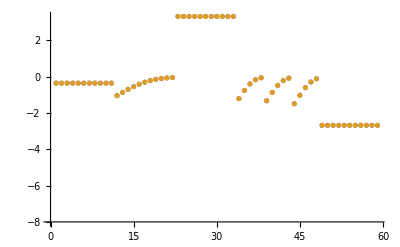

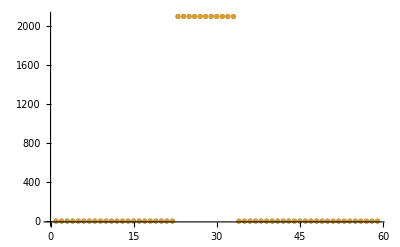

```mathematica
dataSetI=5;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

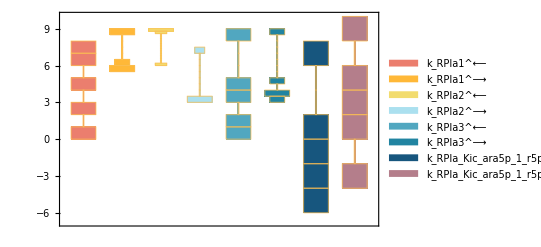

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

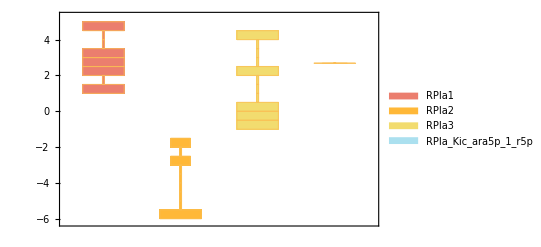

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

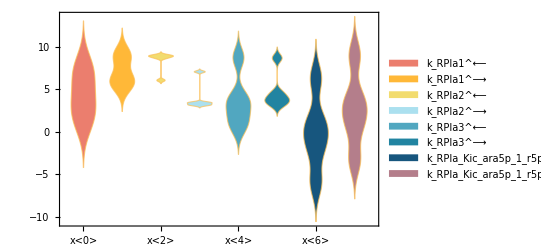

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

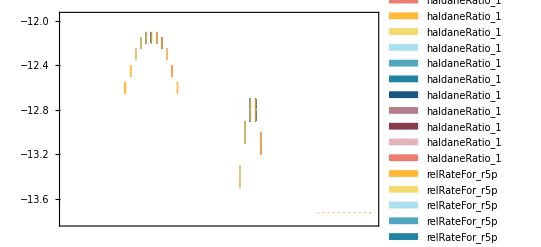

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

backCalculateKms[(r5p^c⇌ru5p__D^c)^RPIa,{{1,r5p,0.0031,{0.0029,0.0033},{},M,7.5,37,{{trishcl,0.05}},{}}},{(r5p^c k_RPIa1^⟶ (k_RPIa2^⟶+k_RPIa3^⟵+k_RPIa3^⟶) k_RPIa_Kic_ara5p_1_r5p^⟵)/(r5p^c k_RPIa1^⟶ (k_RPIa2^⟶+k_RPIa3^⟵+k_RPIa3^⟶) k_RPIa_Kic_ara5p_1_r5p^⟵+k_RPIa1^⟵ (k_RPIa2^⟶+k_RPIa3^⟵) (k_RPIa_Kic_ara5p_1_r5p^⟵+ara5p^c k_RPIa_Kic_ara5p_1_r5p^⟶)+k_RPIa2^⟶ k_RPIa3^⟶ (k_RPIa_Kic_ara5p_1_r5p^⟵+ara5p^c k_RPIa_Kic_ara5p_1_r5p^⟶))},{(ru5p__D^c k_RPIa2^⟵ (k_RPIa1^⟵+k_RPIa3^⟵+k_RPIa3^⟶) k_RPIa_Kic_ara5p_1_r5p^⟵)/(ru5p__D^c k_RPIa2^⟵ (k_RPIa1^⟵+k_RPIa3^⟵+k_RPIa3^⟶) k_RPIa_Kic_ara5p_1_r5p^⟵+(k_RPIa1^⟵ (k_RPIa2^⟶+k_RPIa3^⟵)+k_RPIa2^⟶ k_RPIa3^⟶) (k_RPIa_Kic_ara5p_1_r5p^⟵+ara5p^c k_RPIa_Kic_ara5p_1_r5p^⟶))},{r5p^c→∞},{ru5p__D^c→∞},{k_RPIa1^⟵→8.39374×10^7,k_RPIa1^⟶→8.93866×10^8,k_RPIa2^⟵→4.8134×10^8,k_RPIa2^⟶→1422.43,k_RPIa3^⟵→2.96754,k_RPIa3^⟶→41773.7,k_RPIa_Kic_ara5p_1_r5p^⟵→0.67409,k_RPIa_Kic_ara5p_1_r5p^⟶→320.995},1,RPIa]

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
2100. | (7.1607×10^16)/(2.60294×10^13+1.19704×10^11 (0.67409+320.995 ara5p^c)) | 0.047619 Abs[2100.-(7.1607×10^16)/(2.60294×10^13+1.19704×10^11 (0.67409+320.995 ara5p^c))]

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.443 | 0.443 | 9.04907×10^-10

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.443 | 0.443 | 9.04907×10^-10

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

backCalculateKic[{{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt,0.443},{1,0.00031,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.0909091},{1,0.000491317,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.136807},{1,0.000778685,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.20076},{1,0.00123413,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.284747},{1,0.00195597,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.386863},{1,0.0031,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.5},{1,0.00491317,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.613137},{1,0.00778685,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.715253},{1,0.0123413,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.79924},{1,0.0195597,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.863193},{1,0.031,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.909091},{1,0.01,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt,2100.},{1,0.01,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt,2100.},{1,0.01,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt,2100.},{1,0.01,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt,2100.},{1,0.01,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt,2100.},{1,0.01,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt,2100.},{1,0.01,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt,2100.},{1,0.01,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt,2100.},{1,0.01,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt,2100.},{1,0.01,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt,2100.},{1,0.01,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt,2100.},{1,0.00031,0,0.00105,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.0625},{1,0.000980306,0,0.00105,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.174112},{1,0.0031,0,0.00105,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.4},{1,0.00980306,0,0.00105,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.678269},{1,0.031,0,0.00105,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.869565},{1,0.00031,0,0.0021,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.047619},{1,0.000980306,0,0.0021,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.136527},{1,0.0031,0,0.0021,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.333333},{1,0.00980306,0,0.0021,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.612574},{1,0.031,0,0.0021,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.833333},{1,0.00031,0,0.0042,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.0322581},{1,0.000980306,0,0.0042,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.0953577},{1,0.0031,0,0.0042,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.25},{1,0.00980306,0,0.0042,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.513167},{1,0.031,0,0.0042,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.769231},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt,0.0021},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt,0.0021},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt,0.0021},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt,0.0021},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt,0.0021},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt,0.0021},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt,0.0021},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt,0.0021},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt,0.0021},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt,0.0021},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt,0.0021}},{5.54294×10^-22,{8.39374×10^7,8.93866×10^8,4.8134×10^8,1422.43,2.96754,41773.7,0.67409,320.995},{0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.0909091,0.136807,0.20076,0.284747,0.386863,0.5,0.613137,0.715253,0.79924,0.863193,0.909091,2100.,2100.,2100.,2100.,2100.,2100.,2100.,2100.,2100.,2100.,2100.,0.0625,0.174112,0.4,0.678269,0.869565,0.047619,0.136527,0.333333,0.612574,0.833333,0.0322581,0.0953577,0.25,0.513167,0.769231,0.0021,0.0021,0.0021,0.0021,0.0021,0.0021,0.0021,0.0021,0.0021,0.0021,0.0021}},{Priority,r5p[c],ru5p__D[c],ara5p[c],param_RPIa_total,param_pH,param_Temp,FileFlag,Target_Data},{{1,Kic,ara5p,0.0021,{0.0012,0.003},{},{{Competitve,r5p,0.0031}},M,7.5,37,{{trishcl,0.05}},{}}}]

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

backCalculateKiu[{{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/haldaneRatio_1.txt,0.443},{1,0.00031,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.0909091},{1,0.000491317,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.136807},{1,0.000778685,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.20076},{1,0.00123413,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.284747},{1,0.00195597,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.386863},{1,0.0031,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.5},{1,0.00491317,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.613137},{1,0.00778685,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.715253},{1,0.0123413,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.79924},{1,0.0195597,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.863193},{1,0.031,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.909091},{1,0.01,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt,2100.},{1,0.01,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt,2100.},{1,0.01,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt,2100.},{1,0.01,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt,2100.},{1,0.01,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt,2100.},{1,0.01,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt,2100.},{1,0.01,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt,2100.},{1,0.01,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt,2100.},{1,0.01,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt,2100.},{1,0.01,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt,2100.},{1,0.01,0,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/absRateFor.txt,2100.},{1,0.00031,0,0.00105,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.0625},{1,0.000980306,0,0.00105,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.174112},{1,0.0031,0,0.00105,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.4},{1,0.00980306,0,0.00105,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.678269},{1,0.031,0,0.00105,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.869565},{1,0.00031,0,0.0021,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.047619},{1,0.000980306,0,0.0021,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.136527},{1,0.0031,0,0.0021,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.333333},{1,0.00980306,0,0.0021,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.612574},{1,0.031,0,0.0021,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.833333},{1,0.00031,0,0.0042,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.0322581},{1,0.000980306,0,0.0042,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.0953577},{1,0.0031,0,0.0042,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.25},{1,0.00980306,0,0.0042,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.513167},{1,0.031,0,0.0042,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/relRateFor_r5p.txt,0.769231},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt,0.0021},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt,0.0021},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt,0.0021},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt,0.0021},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt,0.0021},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt,0.0021},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt,0.0021},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt,0.0021},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt,0.0021},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt,0.0021},{1,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIa_typeII/input/inhibRatio_ara5p_1.txt,0.0021}},{5.54294×10^-22,{8.39374×10^7,8.93866×10^8,4.8134×10^8,1422.43,2.96754,41773.7,0.67409,320.995},{0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.0909091,0.136807,0.20076,0.284747,0.386863,0.5,0.613137,0.715253,0.79924,0.863193,0.909091,2100.,2100.,2100.,2100.,2100.,2100.,2100.,2100.,2100.,2100.,2100.,0.0625,0.174112,0.4,0.678269,0.869565,0.047619,0.136527,0.333333,0.612574,0.833333,0.0322581,0.0953577,0.25,0.513167,0.769231,0.0021,0.0021,0.0021,0.0021,0.0021,0.0021,0.0021,0.0021,0.0021,0.0021,0.0021}},{Priority,r5p[c],ru5p__D[c],ara5p[c],param_RPIa_total,param_pH,param_Temp,FileFlag,Target_Data},{{1,Kic,ara5p,0.0021,{0.0012,0.003},{},{{Competitve,r5p,0.0031}},M,7.5,37,{{trishcl,0.05}},{}}}]

#### Export rate back calculated parameter error distribution

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

Set::shape: Lists {predictedParameters,predictedParameterErrors} and exportPredictedParametersAndErrors[(r5p^c⇌ru5p__D^c)^RPIa,RPIa,«20»,{Priority,r5p[c],ru5p__D[c],ara5p[c],param_RPIa_total,param_pH,param_Temp,FileFlag,Target_Data}] are not the same shape.

Part::take: Cannot take positions 3 through -1 in predictedParameterErrors.

Part::partd: Part specification predictedParameterErrors⟦1⟧ is longer than depth of object.

BoxWhiskerChart::ldata: Transpose[predictedParameterErrors⟦3;;All⟧] is not a valid dataset or list of datasets.

BoxWhiskerChart[Transpose[predictedParameterErrors⟦3;;All⟧],ChartLabels→{predictedParameterErrors⟦1⟧}]